```mathematica
γ=100
```

100

```mathematica
a=2
```

2

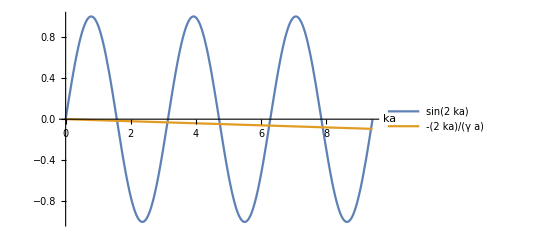

```mathematica
Plot[{Sin[2 ka],-(2 ka)/(γ a)},{ka,0,3Pi},AxesLabel->{ka},PlotLegends->"Expressions"]
```

```mathematica
Clear[k,a, γ,ka]
```

```mathematica
D[-(k+γ Sin[k a]Cos[k a])/(γ Sin[k a]^2),k]
```

(2 a Cot[a k] Csc[a k]^2 (k+γ Cos[a k] Sin[a k]))/γ-(Csc[a k]^2 (1+a γ Cos[a k]^2-a γ Sin[a k]^2))/γ

```mathematica
Simplify[%]
```

((-1+a γ+2 a k Cot[a k]) Csc[a k]^2)/γ

```mathematica
k=Pi/2 /a
```

π/(2 a)

```mathematica
((-1+a γ+2 a k Cot[a k]) Csc[a k]^2)/γ
```

(-1+a γ)/γ

```mathematica
k=Pi/a
```

π/a

```mathematica
((-1+a γ+2 a k Cot[a k]) Csc[a k]^2)/γ
```

ComplexInfinity

```mathematica
Series[Sin[n Pi - (n Pi)/(x a)],{x,Infinity,2}]
```

Sin[n π]-(n π Cos[n π])/x-(n^2 π^2 Sin[n π])/(2 x^2)+O[1/x]^3